```mathematica
code=<|"a"->"·-","b"->"-···","c"->"-·-·","d"->"-··","e"->"·","f"->"··-·","g"->"--·","h"->"····","i"->"··","j"->"·---","k"->"-·-","l"->"·-··","m"->"--","n"->"-·","o"->"---","p"->"·--·","q"->"--·-","r"->"·-·","s"->"···","t"->"-","u"->"··-","v"->"···-","w"->"·--","x"->"-··-","y"->"-·--","z"->"--··","1"->"·----","2"->"··---","3"->"···--","4"->"····-","5"->"·····","6"->"-····","7"->"--···","8"->"---··","9"->"----·","0"->"-----","."->"·-·-·-",","->"--··--","!"->"-·-·--","?"->"··--··", " "->"\n"|>;
withgaps=Map[StringRiffle[Characters[#],"_"]&,code];withpauses=Map[StringInsert[#,"___",-1]&,withgaps];withspace=AssociateTo[withpauses," "->"_______"];replacements=Map[StringReplace[#,{"-"->"111","."->"1","_"->"0"}]&,withspace];

translate[text_] := (
cList = Characters[text];
output = "";
Do[
output = output <> code[c];
output = output <> " "
,{c, cList}];
output
)

obfuscate[morse_]:=(
shorts = {"ă", "ĕ", "ĭ", "ŏ", "ŭ"};
longs = {"ā","ē","ī","ō","ū"};

output = "";
Do[
If[cM == "·",(
output = output <> RandomChoice[shorts];
),If[cM == "-",(
output = output <> RandomChoice[longs];
),
output = output <> cM]];
,{cM, Characters[morse]}];

output
)

framing[text_] := (
cList = Characters[text];
output = {};
Do[
morse = Characters[code[c]];
Do[
If[mC == "·",
output = Join[output, {0, 1}]
];
If[mC == "-",
output = Join[output, {0, 1, 1, 1}]
];
If[mC == "\n",
output = Join[output, {0, 0}]
];
,{mC, morse}];
output = Join[output, {0, 0}];
,{c, cList}];
output = Join[output, {0, 0, 0, 0}];
output
)

message = "lavender";
vowels= obfuscate[translate[message]];
framePattern = framing["crystal"];

translate[message];
frames = Table[Graphics[
{
{EdgeForm[Thick],White,Rectangle[{-8, -1}, {7, 1}]},
If[i == 1,
Text[Style[vowels,FontFamily->"Courier New",Hue[RandomReal[]*.5 + .5], 20]],
Text[Style[vowels,FontFamily->"Courier New",RGBColor[1, 1, 1], 20]]
]
}
], {i, framePattern}];
Export["morse.gif", frames, "DisplayDurations"->.02]
```

morse.gif

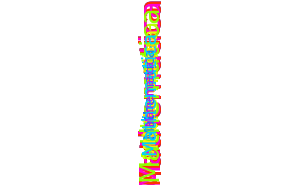

{0.779975,-0.975349}

```mathematica
Graphics[Table[Text[Style["Mathematica",Hue[RandomReal[]],Italic,RandomInteger[{10,30}]],{.5, .5},Automatic, {0, 1}],{20}],AspectRatio->1/GoldenRatio,ImageSize->300]
RandomReal[{-1,1},{2}]
```